10

10

0.2

1

0.1

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

5

3

50

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 50 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

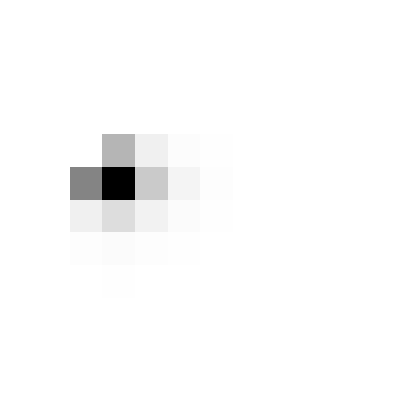

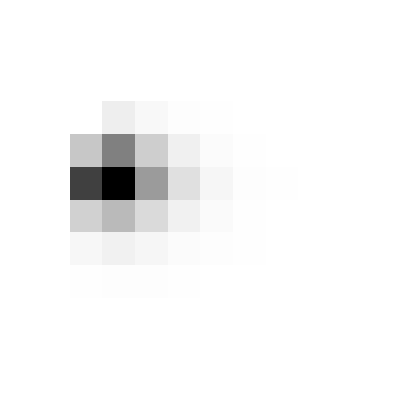

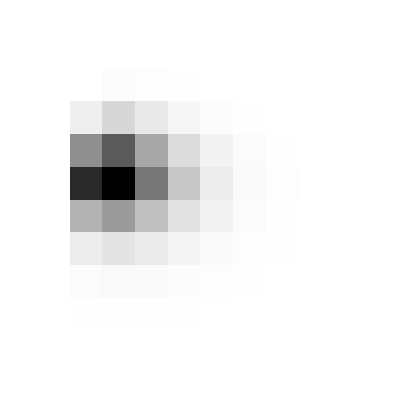

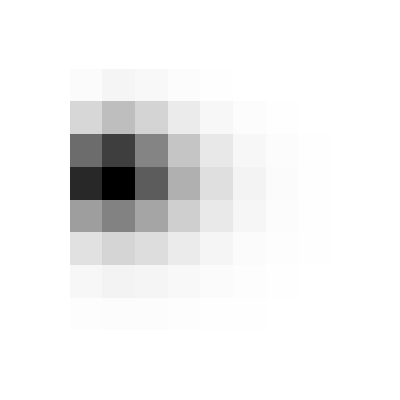

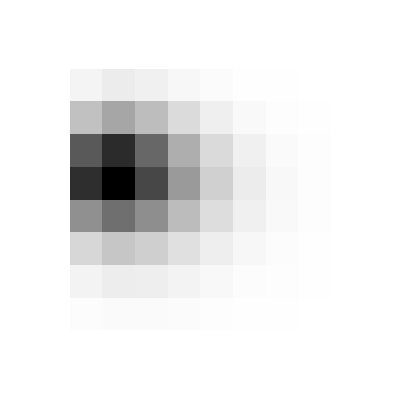

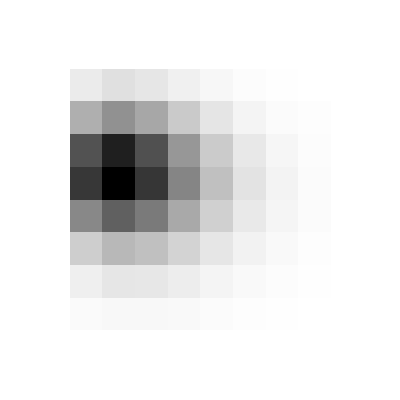

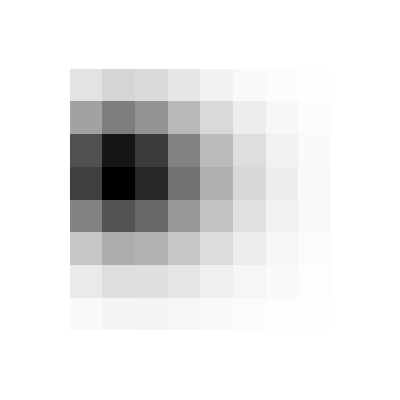

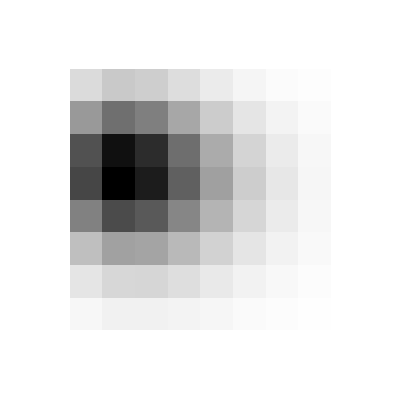

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.243244 | 0.36579 | 0.355097 | 0.270065 | 0.173375 | 0.0978308 | 0.0493288 | 0.020529 | 0
0 | 0.564309 | 0.830424 | 0.798065 | 0.606008 | 0.390703 | 0.222199 | 0.112974 | 0.047095 | 0
0 | 0.844274 | 1.22693 | 1.17501 | 0.895168 | 0.581734 | 0.334413 | 0.171854 | 0.0719533 | 0
0 | 0.872238 | 1.27319 | 1.23207 | 0.952592 | 0.630051 | 0.369137 | 0.193146 | 0.0818293 | 0
0 | 0.644425 | 0.962038 | 0.954726 | 0.7584 | 0.51584 | 0.310771 | 0.166879 | 0.0721121 | 0
0 | 0.367742 | 0.566419 | 0.580806 | 0.477097 | 0.335605 | 0.208957 | 0.115695 | 0.0512463 | 0
0 | 0.171471 | 0.273176 | 0.290017 | 0.246765 | 0.179776 | 0.115828 | 0.0662055 | 0.0301057 | 0
0 | 0.0630369 | 0.103404 | 0.113169 | 0.0993322 | 0.07466 | 0.0495946 | 0.029162 | 0.0135677 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
xMax =Input["Введите предельное значение поля по оси X: ",10]

yMax = Input["Введите предельное значение поля по оси Y: ", 10]
dif = Input["Введите коэффициент диффузии: ", 0.2]
step = Input["Введите шаг итерации: ", 1]
tStep =Input["Введите шаг итерации по времени: ", 0.1]

grid = Array[0 &, {xMax, yMax}]
grid // MatrixForm
xSource = 5
ySource = 3
grid[[xSource, ySource]] = 50

grid // MatrixForm

While[tStep <1.1,
{For[i = 2, i<xMax, i++, For[j = 2, j < yMax, j++, 
{grid[[i,j]] = (grid[[i,j]]+dif*(grid[[i+1,j]]-2*grid[[i,j]]+grid[[i-1,j]])/step), 
grid[[i,j]] = (grid[[i,j]]+dif*(grid[[i,j+1]]-2*grid[[i,j]]+grid[[i,j-1]])/step)}]],
Print[ArrayPlot[grid, FrameLabel->{x,y}]]};
tStep += 0.1
]

grid // MatrixForm
Clear["Global`*"]
```